```mathematica
2-2
```

0

# Physicist's Introduction to Mathematica 6

## Third Edition 2007

## PHYSICS 200

Nicholas Wheeler

REED COLLEGE

## Laboratory 1

## Basic Graphics

Pen-&-ink mathematicians have traditionally found graphics so labor intensive that they have tended to avoid figures whenever possible…and, when a figure could not be avoided, to make do with a merely qualitative representation of the points at issue.  Figures have tended to see service only as expository devices, used to illustrate what was already known, and seldom to be used as aids to discovery.

Mathematica makes the production of accurate figures—of many types—so quick and easy that it should/will become your habit to look to the graphical aspects of problems even before you have fully understood them. The graphical aspects of your mathematical work will therefore assume enlarged importance.  Graphics—formerly an expository device—has become an exploratory tool.

In today's lab we look to some of the most basic graph-generating procedures. In Lab 2 we will look to some more advanced procedures.

### Resources

Your principal reference is at your fingertips. Go to Help > Documentation Center and click on Visualization and Graphics. You will be presented with a list of ten topical heads. Be content for now to open and consider the links made available under the first four of those heads:

• Data Visualization

• Function Visualization

• Dynamnic Visualization

• Options & Styling

Look around to get a sense of the richness of this resource. You might, for example, open Functional Visualization and click on Plot. You will be told how the command works, and be provided with examples. Pay attention also to the tutorials (click on, for example, Basic Plotting), related links and more about that appear at the bottom of the page. You cannot possibly explore all the information placed thus at your command, but these are steps you will have frequent occasion to repeat while familiarizing yourself with Mathematica, and also even after you have become expert, for the small but critical details do tend to slip away.

It might be a good idea to keep a My Graphics notebook, recording your successful accomplishments; it is likely to become your primary reference, a source of templates that you know from your own experience work. Such a notebook would acquire value especially with regard to the correct management of the numerous "options" which are the main source of confusion in this area.

### Simple 2-Dimensional Plotting

```mathematica
?Plot
```

Plot[f,{x,x_min,x_max}] generates a plot of f as a function of x from x_min to x_max. 
Plot[{f_1,f_2,…},{x,x_min,x_max}] plots several functions f_i.

#### First Example

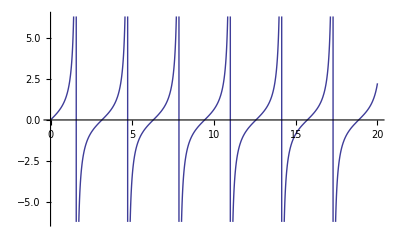

```mathematica
Plot[Tan[x],{x,0,20}]
```

Notice that Mathematica has no trouble at all with the asymptotic infinities.

We look now to a few basic elaborations of the preceding command. First we place the ticks—what are "ticks"?

```mathematica
?Ticks
```

Ticks is an option for graphics functions that specifies tick marks for axes.

—at trigonometrically more natural positions:

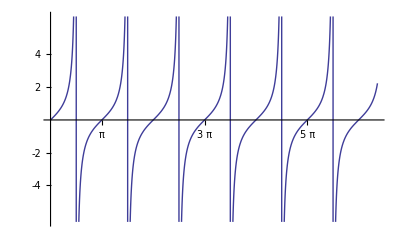

```mathematica
Plot[Tan[x],{x,0,20}, Ticks->{{π,2π,3π,4π,5π,6π},{-4,-2,2,4}}]
```

Next we increase the "thickness" of the curves:

```mathematica
?Thickness
?AbsoluteThickness
```

Thickness[r] is a graphics directive which specifies that lines which follow are to be drawn with thickness r. The thickness r is given as a fraction of the total width of the graphic.

AbsoluteThickness[d] is a graphics directive which specifies that lines which follow are to be drawn with absolute thickness d.

NOTE: Absolute thickness is measured in printer's points: one point = one 72nd of an inch.

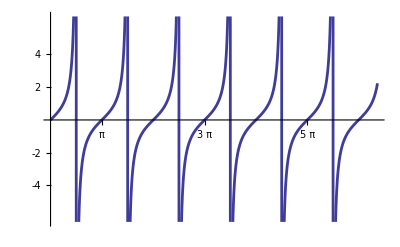

```mathematica
Plot[Tan[x],{x,0,20}, Ticks->{{π,2π,3π,4π,5π,6π},{-4,-2,2,4}}, PlotStyle->{AbsoluteThickness[2]}]
```

Finally, we change the color of the curves:

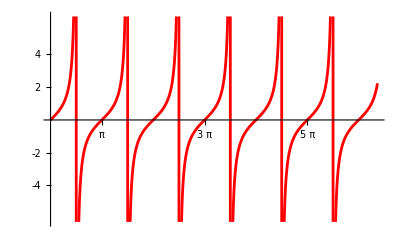

```mathematica
Plot[Tan[x],{x,0,20}, Ticks->{{π,2π,3π,4π,5π,6π},{-4,-2,2,4}}, PlotStyle->{AbsoluteThickness[2],Red}]
```

Red, Green and Blue are basic color attributes. For information about more refined degrees of color control, trace the »s in

```mathematica
?RGBColor
?Hue
```

RGBColor[red,green,blue] is a graphics directive which specifies that objects which follow are to be displayed, if possible, in the color given. 
RGBColor[r,g,b,a] specifies opacity a.

Hue[h] is a graphics directive which specifies that objects which follow are to be displayed, if possible, in a color corresponding to hue h. 
Hue[h,s,b] specifies colors in terms of hue, saturation and brightness. 
Hue[h,s,b,a] specifies opacity a.

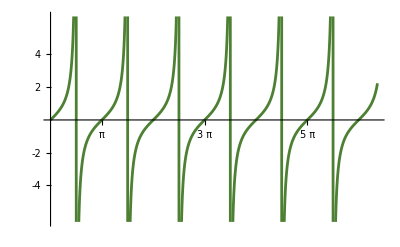

```mathematica
Plot[Tan[x],{x,0,20}, Ticks->{{π,2π,3π,4π,5π,6π},{-4,-2,2,4}}, PlotStyle->{AbsoluteThickness[2],RGBColor[.3,.5,.2]}]
```

NOTE: To create  → while entering a command, type first - (hyphen), then > .

#### Second Example

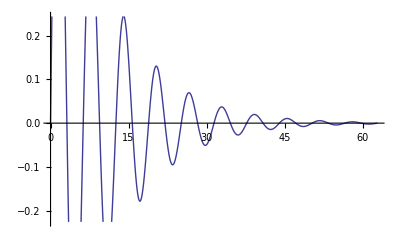

```mathematica
Plot[Sin[t] ⅇ^(-t/10),{t,0,20π}]
```

Mathematica strives automatically to emphasize what it considers to be "the interesting part" of a figure, with the result that it has here clipped off some detail. I give two ways to override that defect:

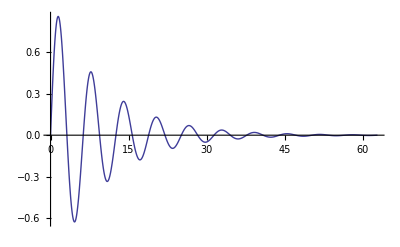

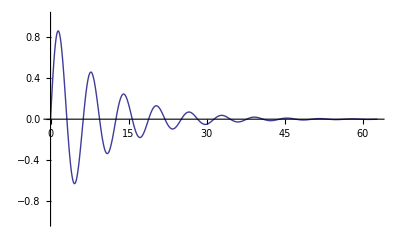

```mathematica
Plot[Sin[t] ⅇ^(-t/10),{t,0,20π}, PlotRange->All]
Plot[Sin[t] ⅇ^(-t/10),{t,0,20π}, PlotRange->{-1,1}]
```

#### Third Example

This example, borrowed from §1.2 of Stan Wagon's Mathematica in Action (2nd edition 1999), provides a taste of "graphical discovery/exploration."

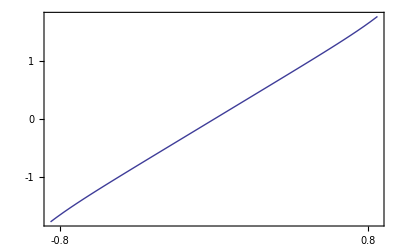

```mathematica
Plot[Sin[x]+ArcSin[x], {x,-0.85,0.85},Frame->True, FrameTicks->{{-0.8,0.8}, {-1,0,1}}]
```

The graph is remarkable for its unexpected linearity. To gain a sense of how linear it truly is, we might proceed as follows: we find the equation of the straight line that approximates the preceding curve in the neighborhood of its mid-section

```mathematica
Clear[a]
```

```mathematica
a=Sin[.5]+ArcSin[.5]
```

1.00302

```mathematica
linear[x_]:=a/(.5)x  (*Equation of a straight line passing through a couple of selected points on the curve*)
```

NOTE the technique used to attach an explanatory remark to the definition.

and then superimpose the curve and line:

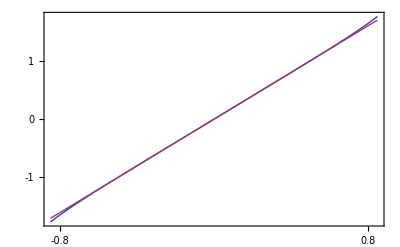

```mathematica
Plot[{Sin[x]+ArcSin[x],linear[x]}, {x,-0.85,0.85},Frame->True, FrameTicks->{{-0.8,0.8}, {-1,0,1}}]
```

which reveals a slight departure from linearity at the ends. The mystery is explained when we command

```mathematica
Series[Sin[x]+ArcSin[x],{x,0,15}]
```

2 x+x^5/12+(2 x^7)/45+(5513 x^9)/181440+(2537 x^11)/113400+(4156001 x^13)/239500800+(285335441 x^15)/20432412000+O[x]^16

and discover that—remarkably—the Maclaurin expansion has no terms of orders 2, 3, or 4. We made first-time use here of the following resource:

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y}] successively finds series expansions with respect to x, then y.

The dangling O[x]^16 is an uninformative annoyance, but is easily  avoided:

```mathematica
Series[Sin[x]+ArcSin[x],{x,0,15}]//Normal
```

2 x+x^5/12+(2 x^7)/45+(5513 x^9)/181440+(2537 x^11)/113400+(4156001 x^13)/239500800+(285335441 x^15)/20432412000

### Filled Plots

Go to Help > Documentation Center, launch a search for ref/Plot (which will take you back to a tutorial notebook you have already seen), scroll down the page a short distance and encounter examples of several kinds of "filled plots." Here follows an example of the utility of that device, taken from some of my own work.

In Gaussian Wavepackets (1998) I had occasion to notice that the following function

```mathematica
sechsquared[x_]:=1/2 Sech[x]^2
```

has all the properties required of a probability distribution: it is everywhere non-negative, and

```mathematica
∫_(-∞)^∞ sechsquared[x]ⅆx
```

1

Moreover

```mathematica
∫_(-∞)^∞ x sechsquared[x]ⅆx
∫_(-∞)^∞ x^2 sechsquared[x]ⅆx
```

0

π^2/12

and when plotted it looks very Gaussian (very "normal"):

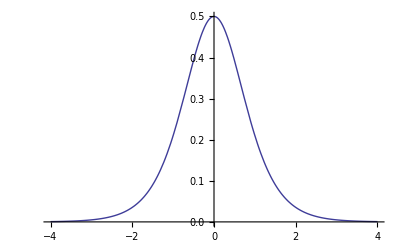

```mathematica
Plot[sechsquared[x],{x,-4,4}]
```

The Gaussian with that same mean (which is to say: is centered at x = 0) and variance σ is defined

```mathematica
gaussian[x_,σ_]:=1/(σ √(2π))Exp[-1/2(x/σ)^2]
```

We want to compare the preceding figure with

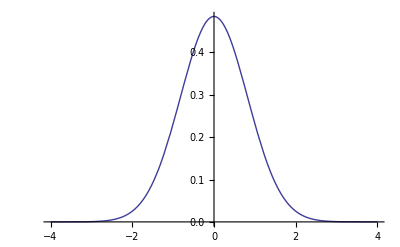

```mathematica
Plot[gaussian[x,π^2/12],{x,-4,4}]
```

so again superimpose the two figures, drawing upon

```mathematica
?Filling
```

Filling is an option for ListPlot, Plot, Plot3D and related functions which specifies what filling to add under points, curves and surfaces.

to construct the command

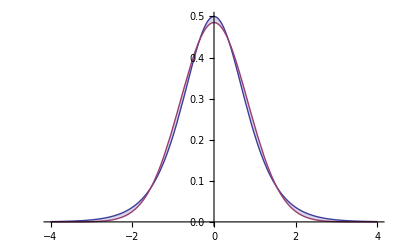

```mathematica
Plot[{sechsquared[x], gaussian[x,π^2/12]}, {x, -4,4}, Filling -> {1 -> {2}}]
```

### Polar Plot

For relevant information, command

```mathematica
?PolarPlot
```

PolarPlot[r,{θ,θ_min,θ_max}] generates a polar plot of a curve with radius r as a function of angle θ.
PolarPlot[{f_1,f_2,…},{θ,θ_min,θ_max}] makes a polar plot of curves with radius functions f_1, f_2, ….

and follow the ≫.

Not infrequently the result of physical calculation lends itself better to polar than to Cartesian graphical representation. For example, the theory of planetary motion (Kepler problem) leads to an equation of the form

r=constant/(1+eccentricity×cos(θ))

of which I illustrate an instance:

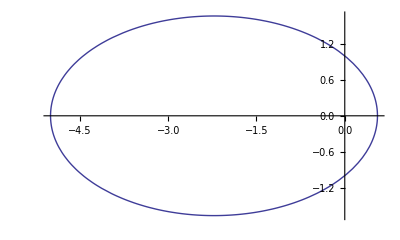

```mathematica
PolarPlot[1/(1+.8Cos[θ]),{θ,0,2π}]
```

Slight adjustment causes the orbit to precess:

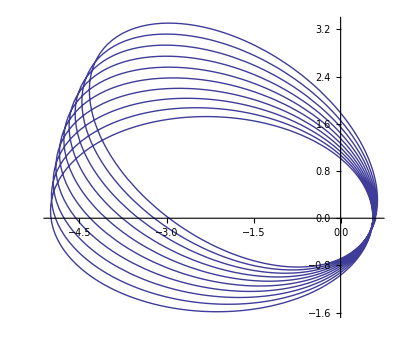

```mathematica
PolarPlot[1/(1+.8Cos[1.01θ]),{θ,0,20π}]
```

Try these further examples of polar plots:

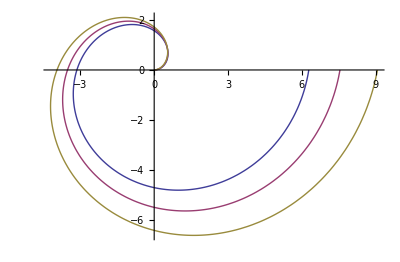

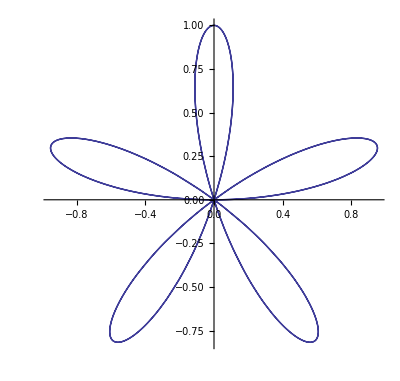

```mathematica
PolarPlot[{t,t^1.1,t^1.2},{t,0,2π}]
PolarPlot[Sin[5θ],{θ,0,2π}]
```

### List Plot

For relevant information, pose the question

```mathematica
?ListPlot
```

ListPlot[{y_1,y_2,…}] plots points corresponding to a list of values, assumed to correspond to x coordinates 1, 2, …. 
ListPlot[{{x_1,y_1},{x_2,y_2},…}] plots a list of points with specified x and y coordinates. 
ListPlot[{list_1,list_2,…}] plots several lists of points.

and again go where the ≫ takes you. I illustrate this graphical technique as it pertains to the familiar Fibonacci numbers, which are available as a built-in resource:

```mathematica
?Fibonacci
```

Fibonacci[n] gives the Fibonacci number F_n. 
Fibonacci[n,x] gives the Fibonacci polynomial F_n(x).

```mathematica
Fibonacci[50]
```

12586269025

Make a table of the first 10 Fibonacci numbers

```mathematica
fib=Table[Fibonacci[n],{n,10}]
```

{1,1,2,3,5,8,13,21,34,55}

and use  ListPlot to display that data graphically:

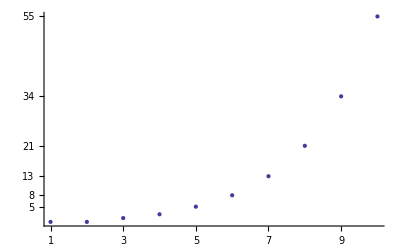

```mathematica
ListPlot[{1,1,2,3,5,8,13,21,34,55},PlotStyle->PointSize[Large], Ticks->{{1,2,3,4,5,6,7,8,9,10},{5,8,13,21,34,55}}]
```

I don't like where Mathematica elected to place the vertical axis, so look at the available options

```mathematica
Options[ListPlot]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,InterpolationOrder→None,Joined→False,LabelStyle→{},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

which leads me to inquire about the precise meaning of

```mathematica
?AxesOrigin
```

AxesOrigin is an option for two-dimensional graphics functions which specifies where any axes drawn should cross.

and therefore to make this adjusted command:

```mathematica
ListPlot[{1,1,2,3,5,8,13,21,34,55},PlotStyle->PointSize[Large], Ticks->{{1,2,3,4,5,6,7,8,9,10},{5,8,13,21,34,55}},AxesOrigin->{0,0}]
```

-Graphics-

### Parametric Plot

Pose the question

```mathematica
?ParametricPlot
```

ParametricPlot[{f_x,f_y},{u,u_min,u_max}] generates a parametric plot of a curve with x and y coordinates f_x and f_y as a function of u. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max}] plots several parametric curves. 
ParametricPlot[{f_x,f_y},{u,u_min,u_max},{v,v_min,v_max}] plots a parametric region. 
ParametricPlot[{{f_x,f_y},{g_x,g_y},…},{u,u_min,u_max},{v,v_min,v_max}] plots several parametric regions.

and follow the ≫. You are led to discription of a very powerful graphic resource, use of which I illustrate with a series of examples:

#### First Example: Simple Cycloid

A circle of unit radius rolls along the x-axis. We are interest in the curve traced by a point P marked on the circumference of the circle. Working from a sketch, we are led to define

```mathematica
x[θ_]:=θ-Sin[θ]
y[θ_]:=1-Cos[θ]
```

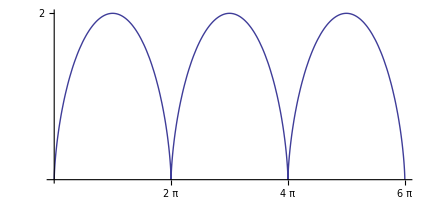

```mathematica
ParametricPlot[{x[θ], y[θ]}, {θ,0,6π}, Ticks->{{2π, 4π, 6π},{2}}]
```

REMARK: One can change the display size a graphical image by clicking on it and dragging a handle of the box that appears: try it!

#### Second Example: Epicycles

The following is taken from Stan Wagon's discussion of an idea developed by Norton Starr (Amherst College): A wheel of given radius turns with given angular velocity. Pinned at its circumference is a second wheel of given radius that turns with given angular velocity.  And pinned to its circumference is a third wheel…etc. We are interested in the motion of a point marked on the circumference of the last wheel.  In a specific instance, Wagon was led thus to the following command/figure:

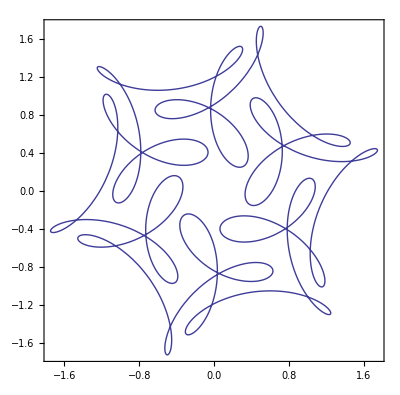

```mathematica
ParametricPlot[{Cos[θ],Sin[θ]}+1/2{Cos[7θ],Sin[7θ]}+1/3{Cos[-17θ+π/2],Sin[-17θ+π/2]},{θ,0,2π},Frame->True]
```

Adjustment of the numerics would, of course, result in different curves.  It is not immediately obvious why the present numerics (1, 7 & —17) generate 6-fold symmetry!

#### Third Example: Lissajous Figures

The following construction is familiar to anyone who has ever played with an oscilloscope:

```mathematica
Clear[a,b,x,y]
```

```mathematica
x[t_,a_,α_]:=a Cos[α t]
y[t_,b_,β_,δ_]:=b Cos[β t+δ]
```

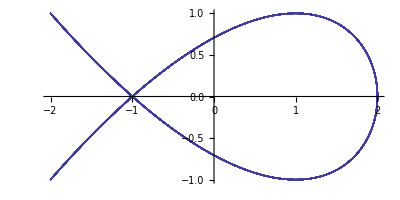

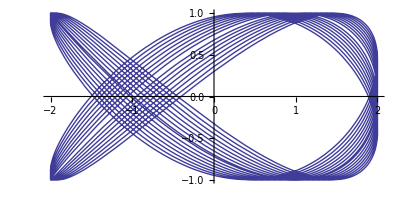

```mathematica
ParametricPlot[{x[t,2,2],y[t,1,3.00,π/2]},{t,0,16π},AspectRatio->Automatic]

ParametricPlot[{x[t,2,2],y[t,1,3.01,π/2]},{t,0,16π},AspectRatio->Automatic]
```

### 3-Dimensional Plotting

For relevant information, proceed in the usual manner: pose the question

```mathematica
?Plot3D
```

Plot3D[f,{x,x_min,x_max},{y,y_min,y_max}] generates a three-dimensional plot of f as a function of x and y. 
Plot3D[{f_1,f_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several functions.

and follow the ≫.

The basic command is again very simple:

```mathematica
Clear[f]
```

```mathematica
f[x_,y_]:=(x^2+3 y^2)ⅇ^(1-x^2-y^2)
```

We will find it convenient to give a name to the resulting 3D figure:

```mathematica
doublehump=Plot3D[f[x,y],{x,-2,2},{y,-3,3}]
```

```mathematica
Show[doublehump]
```

-Graphics3D-

Now something absolutely amazing—new to v.6: place the cursor on the figure, it turns into a pair of arrows, chasing one another around an ellipse. Drag that modified cursor around and the figure revolves, so that you can few the plotted surface from all angles, from above and below!

Plot3D is endowed with a great many control options

```mathematica
Options[Plot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},BoundaryStyle→GrayLevel[0],Boxed→True,BoxRatios→{1,1,0.4},BoxStyle→{},ClippingStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,FaceGrids→None,FaceGridsStyle→{},Filling→None,FillingStyle→Opacity[0.5],FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},Lighting→Automatic,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#1&,#2&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Full,Automatic},PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},ViewAngle→Automatic,ViewCenter→{1/2,1/2,1/2},ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},WorkingPrecision→MachinePrecision}

? can be used to obtain information about each of those—look for example at

```mathematica
?Mesh
```

Mesh is an option for Plot3D, DensityPlot and other plotting functions that specifies what mesh should be drawn.

—concerning which in earlier versions of Mathematica one had to acquire a fairly good command. But Plot3D works so sweetly in v.6 that for most purposes one can forget about most of that stuff.

### Spherical Plot

While Plot3D uses Cartesian coordinates to construct 3D surfaces, it is also possible to work directly in spherical coordinates, to construct 3D analogs  of polar  plots.

```mathematica
?SphericalPlot3D
```

RowBox[{"SphericalPlot3D", "[", RowBox[{StyleBox["r", "TI"], ",", RowBox[{"{", RowBox[{StyleBox["θ", "TR"], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["ϕ", "TR"], ",", SubscriptBox[StyleBox["ϕ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["ϕ", "TR"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a 3D plot with a spherical radius r as a function of spherical coordinates θ and ϕ. 
RowBox[{"SphericalPlot3D", "[", RowBox[{RowBox[{"{", RowBox[{SubscriptBox[StyleBox["r", "TI"], StyleBox["1", "TR"]], ",", SubscriptBox[StyleBox["r", "TI"], StyleBox["2", "TR"]], ",", StyleBox["…", "TR"]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["θ", "TR"], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["θ", "TR"], StyleBox["max", "TI"]]}], "}"}], ",", RowBox[{"{", RowBox[{StyleBox["ϕ", "TR"], ",", SubscriptBox[StyleBox["ϕ", "TR"], StyleBox["min", "TI"]], ",", SubscriptBox[StyleBox["ϕ", "TR"], StyleBox["max", "TI"]]}], "}"}]}], "]"}] generates a 3D spherical plot with multiple surfaces.

```mathematica
Options[SphericalPlot3D]
```

{AlignmentPoint→Center,AspectRatio→Automatic,Axes→True,AxesEdge→Automatic,AxesLabel→None,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},Boxed→True,BoxRatios→Automatic,BoxStyle→{},ColorOutput→Automatic,ContentSelectable→Automatic,ControllerLinking→Automatic,ControllerMethod→Automatic,ControllerPath→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},FaceGrids→None,FaceGridsStyle→{},FormatType:>TraditionalForm,ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,LabelStyle→{},Lighting→Automatic,Method→Automatic,PlotLabel→None,PlotRange→Automatic,PlotRangePadding→Automatic,PlotRegion→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotationAction→Fit,SphericalRegion→False,Ticks→Automatic,TicksStyle→{},ViewAngle→Automatic,ViewCenter→{1/2,1/2,1/2},ViewMatrix→Automatic,ViewPoint→{1.3,-2.4,2.},ViewRange→All,ViewVector→Automatic,ViewVertical→{0,0,1},BoundaryStyle→Automatic,ColorFunction→Automatic,ColorFunctionScaling→True,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,MaxRecursion→Automatic,Mesh→Automatic,MeshFunctions→{#4&,#5&},MeshShading→None,MeshStyle→Automatic,NormalsFunction→Automatic,PerformanceGoal:>$PerformanceGoal,PlotPoints→Automatic,PlotStyle→Automatic,RegionFunction→(True&),WorkingPrecision→MachinePrecision}

#### First Example

```mathematica
SphericalPlot3D[2,{ϕ,0,π},{θ,0,π}, Boxed->False, Axes->False]
```

-Graphics3D-

NOTE that the mouse can again be used to adjust the orientation of the figure.

#### Second Example

The following figure is so pretty that Bruce & Eve Torrence put it on the cover of their The Student's Introduction to Mathematica (1999).

```mathematica
SphericalPlot3D[θ,{ϕ,0,π}, {θ,0,(7π)/2},Boxed->False,
Axes->False]
```

-Graphics3D-

Use the mouse to give that a spin!

#### A Physical Example: Larmor Radiation Pattern

The directional dependence of the radiation emitted by an accelerated charge is (in non-relativistic approximation) given by Joseph Larmor's "sine squared" law (see Griffiths, Introduction to Electrodynamics §9.2.3).  First we plot the distribution

```mathematica
larmor=SphericalPlot3D[Sin[ϕ]^2,{ϕ,0,π},{θ,0,π},
Boxed->False,
Axes->False]
```

-Graphics3D-

Then we construct a line indicating the direction in which the charged particle has been assumed to be accelerating:

```mathematica
acceleration=Graphics3D[{AbsoluteThickness[2],RGBColor[1,0,0],Line[{{0,0,0},{0,0,1}}]},Boxed->False ]
```

-Graphics3D-

And finally we superimpose the two figures:

```mathematica
Show[{larmor, acceleration}]
```

-Graphics3D-

Again, give it a spin!

### ListPlot3D

I have never had occasion to use this resource, which—since it can be read about at

```mathematica
?ListPlot3D
```

ListPlot3D[array] generates a three-dimensional plot of a surface representing an array of height values. 
ListPlot3D[{{x_1,y_1,z_1},{x_2,y_2,z_2},…}] generates a plot of the surface with heights z_i at positions {x_i,y_i}. 
ListPlot3D[{data_1,data_2,…}] plots the surfaces corresponding to each of the data_i.

—I am content to pass over in silence. The following resource is, on the other hand, often indespensible.

### ParametricPlot3D

```mathematica
?ParametricPlot3D
```

ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max}] produces a three-dimensional space curve parametrized by a variable u which runs from u_min to u_max. 
ParametricPlot3D[{f_x,f_y,f_z},{u,u_min,u_max},{v,v_min,v_max}] produces a three-dimensional surface parametrized by u and v. 
ParametricPlot3D[{{f_x,f_y,f_z},{g_x,g_y,g_z}…}…] plots several objects together.

#### First Example: A Space Curve

```mathematica
Clear[x,y,z,t]
```

Let

```mathematica
x[t_]:=t/10 Sin[10 t]
y[t_]:=t/10 Cos[10 t]
z[t_]:=t ⅇ^(-t/10)
```

describe the t-parameterized curve in 3-space (which might, for example, refer to the motion of a mathematical point or physical particle). Command

```mathematica
ParametricPlot3D[{x[t],y[t],z[t]},{t,0,10}]
```

-Graphics3D-

Use the mouse to examine the curve from various angles.

#### Second Example: Sector of a Spherical Shell

It takes two parameters to identify the points on a surface; here we use co-latitude θ and longitude ϕ to parameterize the points on the surface of a sphere:

```mathematica
x[ϕ_,θ_]:=Sin[θ]Cos[ϕ]
y[ϕ_,θ_]:=Sin[θ]Sin[ϕ]
z[ϕ_,θ_]:=Cos[θ]
```

```mathematica
ParametricPlot3D[{x[ϕ,θ],y[ϕ,θ],z[ϕ,θ]},
{ϕ,0,(3π)/2},{θ,π/20,(19π)/20},
Boxed->False, Axes->None]
```

-Graphics3D-

#### Third Example: Torus

Here is a variant of the same basic idea:

```mathematica
Clear[x,y,z,u,v]
```

REMARK: The fact that u and v were blue before we entered the Clear command indicated that they were already clear. After execution of the command all the variables in question became blue (= clear).

We can, if we wish, consider

```mathematica
x[u_,v_]:=Cos[u](2+Cos[v])
y[u_,v_]:=Sin[u](2+Cos[v])
z[u_,v_]:=Sin[v]
```

to be components of a single vector-valued function of two parameters:

```mathematica
Φ[u_,v_]:={x[u,v],y[u,v],z[u,v]}
```

We ask Mathematica to show all the positions that such a vector can assume:

```mathematica
ParametricPlot3D[Φ[u,v],{u,-1/6 π,3/2 π},{v,0,2π},Boxed->False, Axes->None]
```

-Graphics3D-

### 2D Projections of 3D Surfaces

Though my subtitle might be interpreted to refer to the screen display of a 3-dimensional surface, such as we have just been viewing, what I have in mind is more like the relation of a topographic map to the 3D model of a mountain range. In this connection, Mathematica provides two distinct resources: DensityPlot and ContourPlot.

We have already had occasion to consider how Plot3D displays the function:

```mathematica
f[x_,y_]:=(x^2+3 y^2)ⅇ^(1-x^2-y^2)
```

```mathematica
Plot3D[f[x,y],{x,-2,2},{y,-3,3}]
```

-Graphics3D-

Look now to the following alternative displays of the same information:

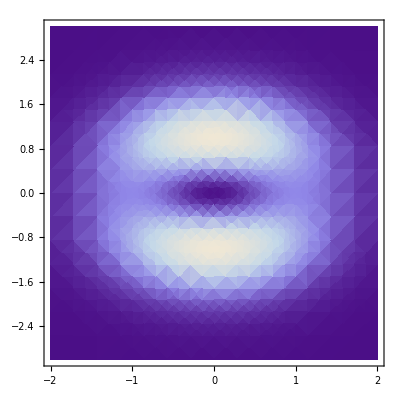

```mathematica
DensityPlot[f[x,y],{x,-2,2},{y,-3,3}]
```

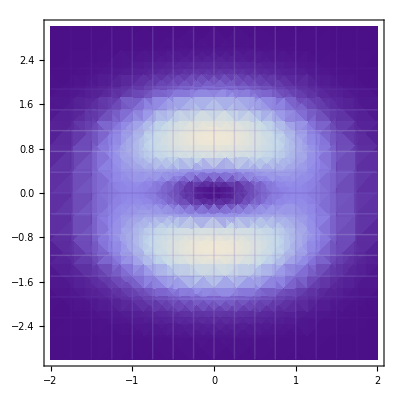

```mathematica
DensityPlot[f[x,y],{x,-2,2},{y,-3,3}, Mesh->15]
```

```mathematica
?ColorFunction
```

ColorFunction is an option for graphics functions which specifies a function to apply to determine colors of elements.

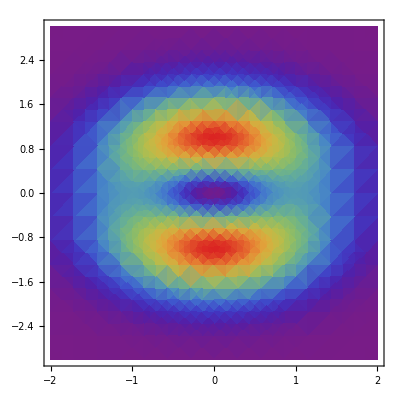

```mathematica
DensityPlot[f[x,y],{x,-2,2},{y,-3,3}, ColorFunction->"Rainbow"]
```

```mathematica
?ContourPlot
```

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a contour plot of f as a function of x and y. 
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}] plots contour lines for which f=g. 
ContourPlot[{f_1==g_1,f_2==g_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several contour lines.

SUGGESTION: Go where  the ≫ takes you and look particularly to the Neat Examples.

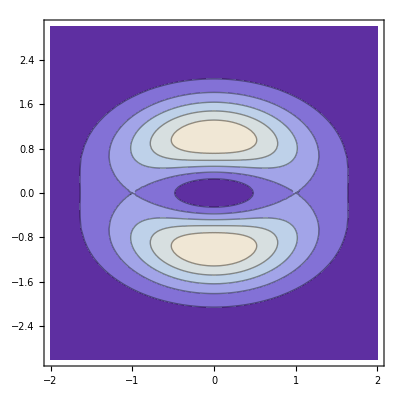

```mathematica
ContourPlot[f[x,y],{x,-2,2},{y,-3,3}]
```

Use the mouse to make the arrow point to one of the contour lines: a little box then announces the value that the function assumes on that contour.

ContourPlot has comes with many options. Below I show the effect of exercising a couple of them:

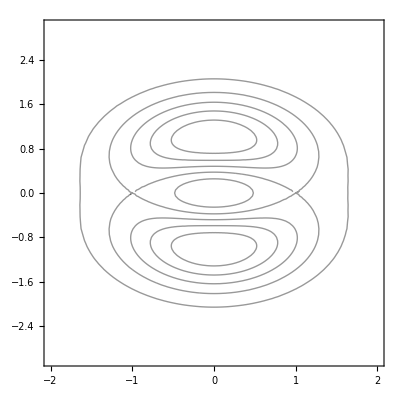

```mathematica
ContourPlot[f[x,y],{x,-2,2},{y,-3,3}, ContourShading->None]
```

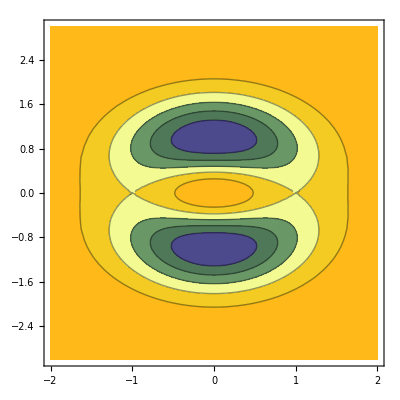

```mathematica
ContourPlot[f[x,y],{x,-2,2},{y,-3,3}, ContourShading->ColorData[35,"ColorList"]]
```

In Mathematica 6 has been enabled also to plot the solutions of equations in two variables. In previous versions of Mathematica this important capability was assigned to the (now obsolete) command ImplicitPlot, which was activated only by importation of a standard package, and never worked very well (was slow, often led to computer crashes).

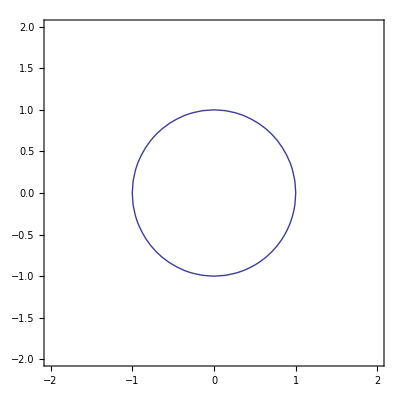

```mathematica
ContourPlot[x^2+y^2==1, {x,-2,2},{y,-2,2}]
```

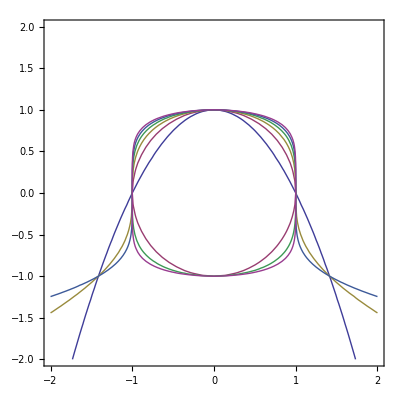

```mathematica
ContourPlot[{x^2+y^1==1,x^2+y^2==1,x^2+y^3==1,x^2+y^4==1,x^2+y^5==1,x^2+y^6==1}, {x,-2,2},{y,-2,2}]
```

#### Example: Eigenstates of a Particle in a Triangular Box

Several years ago I had occasion ("2-dimensional 'particle-in-a-box' problems in quantum mechanics" (1997)) to study the quantum mechanics of particles confined to the interior of polygonal boxes of various favorable shapes.  The 45-45-90 box led to eigenfunctions of a form which I first describe and then plot:

```mathematica
Clear[m,n,x,y]
```

```mathematica
boxfunction[x_,y_,m_,n_]:=Sin[m π x]Sin[n π y]-Sin[n π x]Sin[m π y]
```

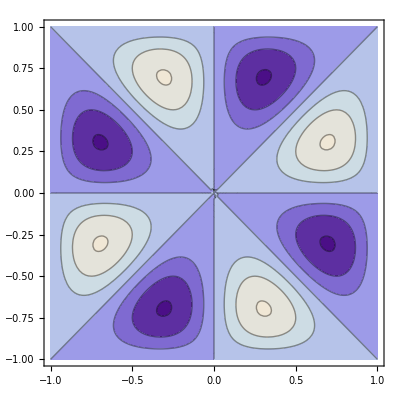
{2.29179,-Graphics-}

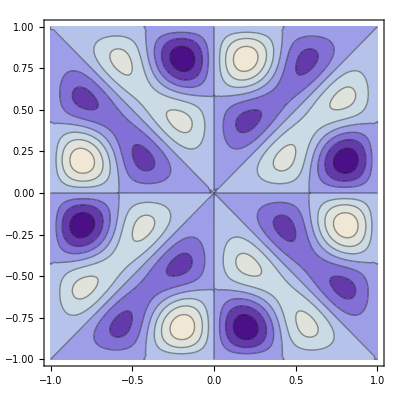
{4.14287,-Graphics-}

{12.1854,-Graphics-}

```mathematica
groundstate=ContourPlot[boxfunction[x,y,1,2],{x,-1,1},{y,-1,1}]//Timing

excitedstate=ContourPlot[boxfunction[x,y,2,3],{x,-1,1},{y,-1,1}]//Timing

highlyexcitedstate=ContourPlot[boxfunction[x,y,11,15],{x,-1,1},{y,-1,1}]//Timing
```

The Timing command resulted in figures of reduced size, so I eliminate that command:

```mathematica
highlyexcitedstate=ContourPlot[boxfunction[x,y,11,15],{x,-1,1},{y,-1,1}]
```

-Graphics-